Levent Batakci - 9/25/2024
AMATH 573 - Homework 1

Problem 1.8.4

```mathematica
f1[x_,t_]= Log[1+Exp[k1*x-k1^3*t+a]];
u1[x_,t_] = 12 * D[f1[x,t],{x,2}];
u1[x,t]
Simplify[u1[x,t]]
```

12 (-(ⅇ^(2 a-2 k1^3 t+2 k1 x) k1^2)/((1+ⅇ^(a-k1^3 t+k1 x))^2)+(ⅇ^(a-k1^3 t+k1 x) k1^2)/(1+ⅇ^(a-k1^3 t+k1 x)))

(12 ⅇ^(a+k1^3 t+k1 x) k1^2)/((ⅇ^(k1^3 t)+ⅇ^(a+k1 x))^2)

```mathematica
f2[x_,t_]= Log[1+Exp[k1*x-k1^3*t+a] + Exp[k2*x-k2^3*t+b] + ((k1-k2)/(k1+k2))^2*Exp[k1*x-k1^3*t+a+k2*x-k2^3*t+b]];
u2[x_,t_] = 12 * D[f2[x,t],{x,2}];
u2[x,t];
Simplify[D[u2[x,t],t] + u2[x,t]*D[u2[x,t],x] + D[u2[x,t],{x,3}]]
```

0

Problem 1.8 .6

```mathematica
theta[x_,t_] = 1 + a*Exp[-k1*x+n*k1^2*t]+b*Exp[-k2*x+n*k2^2*t];
u[x_,t_] = -2*n*D[theta[x,t],x]/theta[x,t]
Simplify[u[x,t]]
```

-(2 (-a ⅇ^(k1^2 n t-k1 x) k1-b ⅇ^(k2^2 n t-k2 x) k2) n)/(1+a ⅇ^(k1^2 n t-k1 x)+b ⅇ^(k2^2 n t-k2 x))

(2 (a ⅇ^(k1^2 n t+k2 x) k1+b ⅇ^(k2^2 n t+k1 x) k2) n)/(ⅇ^((k1+k2) x)+b ⅇ^(k2^2 n t+k1 x)+a ⅇ^(k1^2 n t+k2 x))

```mathematica
Problem 1.8.4, Wild Observation
In the 2-soliton solution, there is an interesting phenomena where the further-back wave tracks the location of the corresponding single soliton solution of the same parameters, perfectly. The collision messes nothing up, and the transition is seamless. Can we show this algebraically?
```

12 ((ⅇ^(a-k1^3 t+k1 x) k1^2+ⅇ^(a+b-k1^3 t-k2^3 t+k1 x+k2 x) (k1-k2)^2+ⅇ^(b-k2^3 t+k2 x) k2^2)/(1+ⅇ^(a-k1^3 t+k1 x)+ⅇ^(b-k2^3 t+k2 x)+(ⅇ^(a+b-k1^3 t-k2^3 t+k1 x+k2 x) (k1-k2)^2)/(k1+k2)^2)-((ⅇ^(a-k1^3 t+k1 x) k1+ⅇ^(b-k2^3 t+k2 x) k2+(ⅇ^(a+b-k1^3 t-k2^3 t+k1 x+k2 x) (k1-k2)^2)/(k1+k2))^2)/((1+ⅇ^(a-k1^3 t+k1 x)+ⅇ^(b-k2^3 t+k2 x)+(ⅇ^(a+b-k1^3 t-k2^3 t+k1 x+k2 x) (k1-k2)^2)/(k1+k2)^2)^2))

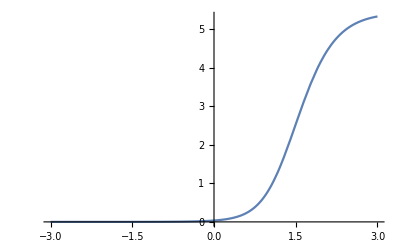

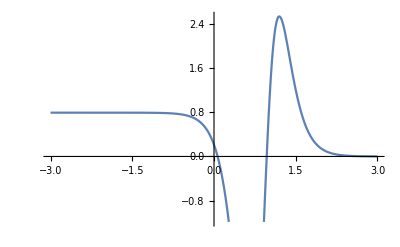

```mathematica
f1[x_,t_]= Log[1+Exp[k1*x-k1^3*t+a]];
u1[x_,t_] = 12 * D[f1[x,t],{x,2}];
f2[x_,t_]= Log[1+Exp[k2*x-k2^3*t+b]];
u2[x_,t_] = 12 * D[f2[x,t],{x,2}];
f3[x_,t_]= Log[1+Exp[k1*x-k1^3*t+a] + Exp[k2*x-k2^3*t+b] + ((k1-k2)/(k1+k2))^2*Exp[k1*x-k1^3*t+a+k2*x-k2^3*t+b]];
u3[x_,t_] = 12 * D[f3[x,t],{x,2}];
DU3[x_,t_] = D[u3[x,t],x];

x1 = Solve[D[u1[x,t],x]==0,x, Reals];
x2 =Solve[D[u2[x,t],x]==0,x, Reals];

u3[x,t]

Simplify[D[u1[x1[x],0],x]];
Simplify[DU3[x,t] /. x2 /.{t -> 1} /. {a -> 0} /. {b -> 0} /. {k1 -> 1.5} /. {k2 -> 1}];
Plot[DU3[x,t] /. x1 /. {a -> 5} /. {b -> 0} /. {k1 -> 19/10} /. {k2 -> 1}, {t,-3,3}]
Plot[DU3[x,t] /. x2 /. {a -> 5} /. {b -> 0} /. {k1 -> 19/10} /. {k2 -> 1}, {t,-3,3}]
```